```mathematica
SetDirectory[NotebookDirectory[]];
(files=FileNames["data/*"])//TableForm
```

data\bla1.csv
data\einzel.csv
data\erstemessung.ods
data\frequenzdoppel.ods
data\hauen1.csv
data\placeholder.txt
data\tem00b.txt
data\tem00.txt
data\tem03.2.bmp
data\tem032b.txt
data\tem032.txt
data\tem03.bmp
data\tem10.bmp
data\tem10b.txt
data\tem10.txt
data\tem20.bmp
data\tem20b.txt
data\tem20.txt
data\zweitemesseung.ods

```mathematica
ρ[r_,w_]:=(2 (r)^2)/w^2;
f[r_,w_,θ_,p_,l_]:=(ρ[r,w])^l*(LaguerreL[p,l,ρ[r,w]])^2(Cos[l*θ])^2 Exp[-ρ[r,w]];
```

```mathematica
Plot3D[f[(x^2+y^2)^0.5,5,ArcTan[y/x],2,1],{x,-10,10},{y,-10,10},Axes->False,ColorFunction->"BlueGreenYellow",PlotRange->All,PlotPoints->40]
```

-Graphics3D-

```mathematica
her[x_,y_,theta_,p_,l_]:=(HermiteH[p,(x*Sin[theta]+y*Cos[theta])]Exp[-(x*Sin[theta]+y*Cos[theta])^2]*HermiteH[l,(x*Cos[theta]-Sin[theta]*y)]Exp[-(x*Cos[theta]-Sin[theta]*y)^2])^2;
```

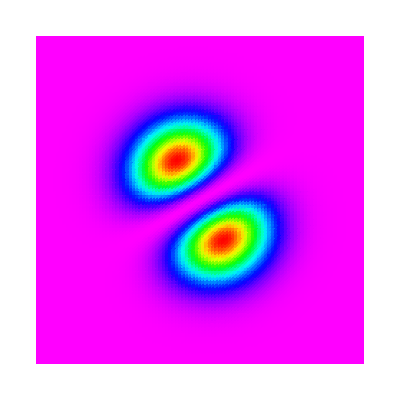
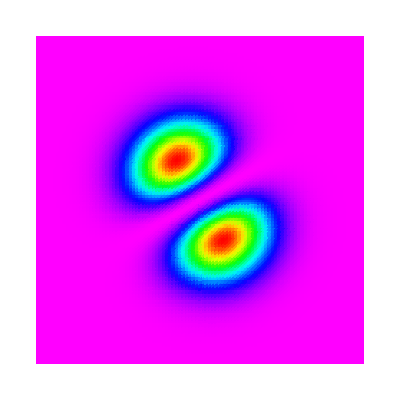

```mathematica
{DensityPlot[her[x,y,Pi/3,0,1],{x,-2.5,2.5},{y,-2.5,2.5},Frame->False,Axes->False,PlotRange->All,MaxRecursion->2,PlotPoints->100,ColorFunction->(Blend[{RGBColor[1,0,1],RGBColor[0,0,1],RGBColor[0,1,1],RGBColor[0,1,0],RGBColor[1,1,0],RGBColor[1,0,0]},#]&)],DensityPlot[f[(x^2+y^2)^0.5,1,ArcTan[y/x]+Pi/3,0,1],{x,-2.5,2.5},{y,-2.5,2.5},Frame->False,Axes->False,PlotRange->All,MaxRecursion->2,PlotPoints->100,ColorFunction->(Blend[{RGBColor[1,0,1],RGBColor[0,0,1],RGBColor[0,1,1],RGBColor[0,1,0],RGBColor[1,1,0],RGBColor[1,0,0]},#]&)]}
```

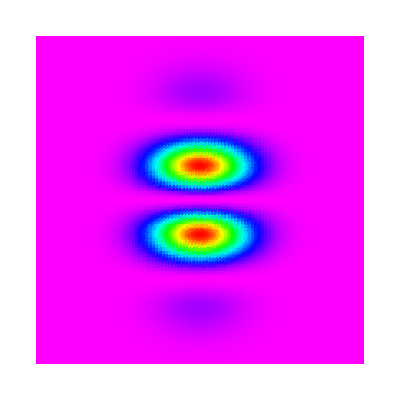
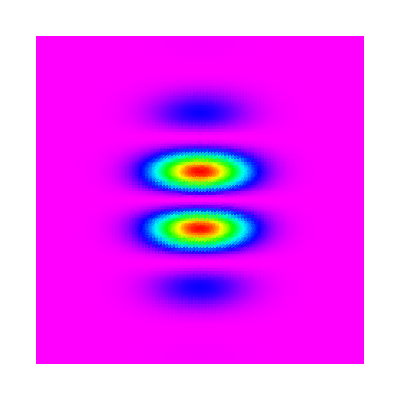
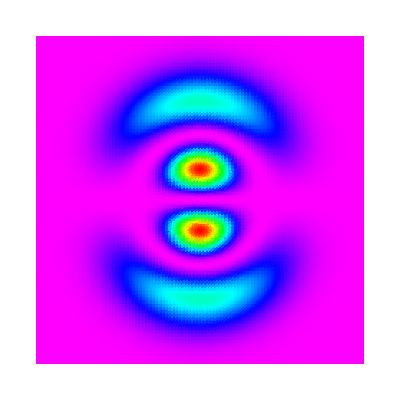
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(DensityPlot[her[x,y,Pi/2,0,#]+0her[x,y,Pi/2,0,0],{x,-2.5,2.5},{y,-2.5,2.5},Frame->False,Axes->False,PlotRange->All,PlotPoints->100,ColorFunction->(Blend[{RGBColor[1,0,1],RGBColor[0,0,1],RGBColor[0,1,1],RGBColor[0,1,0],RGBColor[1,1,0],RGBColor[1,0,0]},#]&)]&/@{3,5,7,9})~Join~{DensityPlot[f[(x^2+y^2)^0.5,1,ArcTan[y/x]-Pi/2,1,1],{x,-2.5,2.5},{y,-2.5,2.5},Frame->False,Axes->False,PlotRange->All,PlotPoints->100,ColorFunction->(Blend[{RGBColor[1,0,1],RGBColor[0,0,1],RGBColor[0,1,1],RGBColor[0,1,0],RGBColor[1,1,0],RGBColor[1,0,0]},#]&)]}
```

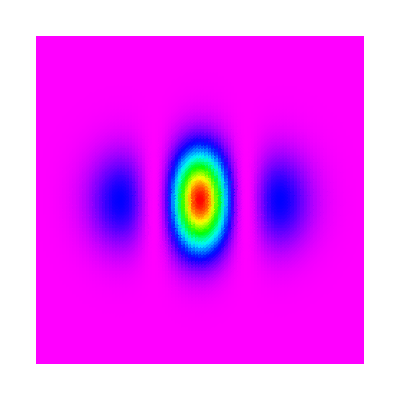
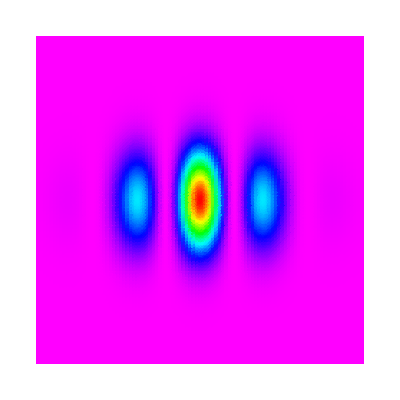
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(DensityPlot[her[x,y,Pi/2,#,0]+0her[x,y,Pi/2,0,0],{x,-2.5,2.5},{y,-2.5,2.5},Frame->False,Axes->False,PlotRange->All,PlotPoints->100,ColorFunction->(Blend[{RGBColor[1,0,1],RGBColor[0,0,1],RGBColor[0,1,1],RGBColor[0,1,0],RGBColor[1,1,0],RGBColor[1,0,0]},#]&)]&/@{2,4,6})~Join~{DensityPlot[f[(x^2+y^2)^0.5,1,ArcTan[y/x],1,0],{x,-2.5,2.5},{y,-2.5,2.5},Frame->False,Axes->False,PlotRange->All,PlotPoints->100,ColorFunction->(Blend[{RGBColor[1,0,1],RGBColor[0,0,1],RGBColor[0,1,1],RGBColor[0,1,0],RGBColor[1,1,0],RGBColor[1,0,0]},#]&)]}
```

```mathematica
{DensityPlot[her[x,y,Pi/2,2,0]+her[x,y,Pi/2,0,2],{x,-2.5,2.5},{y,-2.5,2.5},Frame->False,Axes->False,PlotRange->All,MaxRecursion->2,PlotPoints->100,ColorFunction->(Blend[{RGBColor[1,0,1],RGBColor[0,0,1],RGBColor[0,1,1],RGBColor[0,1,0],RGBColor[1,1,0],RGBColor[1,0,0]},#]&)],
DensityPlot[f[(x^2+y^2)^0.5,0.75,ArcTan[y/x],1,2],{x,-2.5,2.5},{y,-2.5,2.5},Frame->False,Axes->False,PlotRange->All,PlotPoints->100,ColorFunction->(Blend[{RGBColor[1,0,1],RGBColor[0,0,1],RGBColor[0,1,1],RGBColor[0,1,0],RGBColor[1,1,0],RGBColor[1,0,0]},#]&)]}
```

{-Graphics-,-Graphics-}